再谈数字

当你用整数进行计算时，Wolfram 语言会给你一个精确的答案。对于精确的分数，它也是这样做的。

将 1/2+1/3 相加可以得到一个准确的分数答案：

```mathematica
1/2+1/3
```

5/6

很多情况下，你只需要一个数字或小数的近似值。你可以用函数 N(Numerical 的缩写)来获得。

得到一个近似的数值答案：

```mathematica
N[1/2+1/3]
```

0.833333

如果你的输入中有任何小数，Wolfram 语言就会自动给你一个近似的答案。

小数的存在使得结果是近似的：

```mathematica
1.8/2+1/3
```

1.23333

只要在数字的末尾有一个小数点也可以：

```mathematica
1/2.+1/3
```

0.833333

Wolfram 语言可以处理任何大小的数字，只要你的计算机内存足够。

这是 2 的 1000 次方：

```mathematica
2^1000
```

10715086071862673209484250490600018105614048117055336074437503883703510511249361224931983788156958581275946729175531468251871452856923140435984577574698574803934567774824230985421074605062371141877954182153046474983581941267398767559165543946077062914571196477686542167660429831652624386837205668069376

得到一个数字近似值：

```mathematica
N[2^1000]
```

1.07151×10^301

这个近似的形式是用科学记数法给出的。如果你需要输入科学记数法，你可以使用 *^。

用科学记数法来输入一个数字：

```mathematica
2.7*^6
```

2.7×10^6

常用的数字，比如 π(圆周率)，已经内置在 Wolfram 语言中。

得到 π 的近似值：

```mathematica
N[Pi]
```

3.14159

Wolfram 语言可以计算到任意精度，例如，如果需要，它可以计算 π 的小数点后数百万位。

计算包含 250 位有效数字的 π：

```mathematica
N[Pi,250]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930381964428810975665933446128475648233786783165271201909

Wolfram 语言中有许多处理整数的函数。也有许多函数来处理实数。一个例子是 RandomReal，它可以给出随机的实数：

生成位于 0 到 10 的范围内的随机实数：

```mathematica
RandomReal[10]
```

2.08658

生成 5 个随机实数：

```mathematica
Table[RandomReal[10],5]
```

{4.15071,4.81048,8.82945,9.84995,9.08313}

另一种生成 5 个随机实数的方法：

```mathematica
RandomReal[10,5]
```

{6.47318,3.29181,3.57615,8.11204,3.38286}

生成位于 20 到 30 的范围内的随机实数：

```mathematica
RandomReal[{20,30},5]
```

{24.1202,20.1288,20.393,25.6455,20.9268}

Wolfram 语言内置了大量的数学函数，从基本的到非常复杂的。

找到第 100 个素数：

```mathematica
Prime[100]
```

541

找到第 100 万个素数：

```mathematica
Prime[1000000]
```

15485863

绘制前 50 个素数：

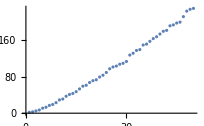

```mathematica
ListPlot[Table[Prime[n],{n,50}]]
```

许多实际场合中常见的三个函数是 Sqrt(平方根)、Log10(以10为底的对数)和 Log(自然对数)。

16 的平方根是 4：

```mathematica
Sqrt[16]
```

4

如果你没有要求一个数字近似值，你就会得到一个精确的公式：

```mathematica
Sqrt[200]
```

10 √2

N 将给出一个数字近似值：

```mathematica
N[Sqrt[200]]
```

14.1421

当你处理那些大小不一的数字时，对数往往很有用。让我们来绘制行星的质量。直接使用 ListPlot，我们会无法知道木星之前的行星的任何情况。但使用 ListLogPlot 能更清楚地显示出相对大小。

创建行星的质量的普通点集图：

```mathematica
ListPlot[EntityClass["Planet",All]["Mass"]]
```

-Graphics-

创建点集对数图：

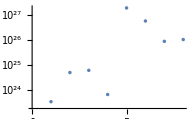

```mathematica
ListLogPlot[EntityClass["Planet",All]["Mass"]]
```

还有几个函数经常出现在一般的编程中。首先，有一个很容易忽略的函数 Abs，它可以找到一个数字的绝对值，或正数部分。

Abs 实际上只是舍弃了负号：

```mathematica
{Abs[3],Abs[-3]}
```

{3,3}

接下来是 Round，它将四舍五入到最近的整数。

Round 将四舍五入到最近的整数：

```mathematica
{Round[3.2],Round[3.4],Round[3.6],Round[3.9]}
```

{3,3,4,4}

另一个非常有用的函数是 Mod。比方说，你数一个小时内的分钟数。当达到 60 分钟时，想从 0 开始，这正是 Mod 完成的功能。

计算一系列数字 对 60 的余数：

```mathematica
{Mod[50,60],Mod[55,60],Mod[60,60],Mod[65,60],Mod[70,60]}
```

{50,55,0,5,10}

词汇

N[expr] |   | 数值近似
Pi |   | 数字 π (pi)≃3.14 
Sqrt[x] |   | 平方根
Log10[x] |   | 以 10 为底的对数
Log[x] |   | 自然对数(ln)
Abs[x] |   | 绝对值(去掉负号)
Round[x] |   | 圆整到最近的整数
Prime[n] |   | 第 n 个素数
Mod[x,n] |   | 模余(“时钟运算”)
RandomReal[max] |   | 介于 0 到 max 之间的随机实数
RandomReal[max,n] |   | n 个随机实数的列表
ListLogPlot[data] |   | 在对数尺度上进行绘制

"共有 14 道习题"
"以及 4 道附加题" | "开始练习 »"

求 √2 的 500 位有效数字。»

| 期望输出： |  
  | 1.4142135623730950488016887242096980785696718753769480731766797379907324784621070388503875343276415727350138462309122970249248360558507372126441214970999358314132226659275055927557999505011527820605714701095599716059702745345968620147285174186408891986095523292304843087143214508397626036279952514079896872533965463318088296406206152583523950547457502877599617298355752203375318570113543746034084988471603868999706990048150305440277903164542478230684929369186215805784631115966687130130156185689872372 |

生成 10 个 0 到 1 之间的随机实数。»

| 期望输出示例： |  
  | {0.981757,0.501571,0.0805282,0.0247074,0.0663221,0.812191,0.929721,0.949164,0.674154,0.0702841} |

用在 0 和 1 之间的随机实数为 x 和 y 坐标的 200 个点创建一个图。»

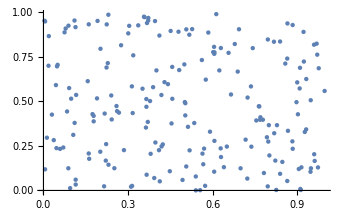
| 期望输出示例： |  
  | -Graphics- |

使用 AnglePath 以及 1000 个 0 到 2π 之间的随机实数来创建一个随机路径图。»

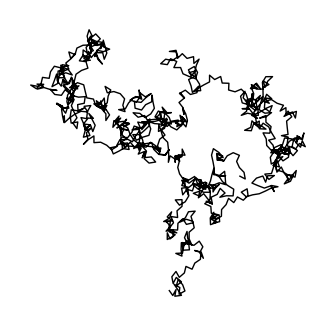
| 期望输出示例： |  
  | -Graphics- |

创建一个 Mod[n^2,10] 的表，其中 n 为 0 到 30。»

| 期望输出： |  
  | {0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0} |

创建 Mod[n^n,10] 的线条图，其中 n 为 1 到 100。»

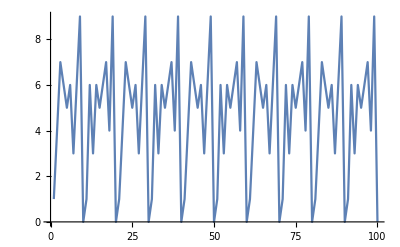
| 期望输出： |  
  | -Graphics- |

创建 π 的前 10 次幂的表，四舍五入为整数。»

| 期望输出： |  
  | {3,10,31,97,306,961,3020,9489,29809,93648} |

通过将 n 与 Mod[n^2,100] 进行连接的图，其中 n 为 0 到 99。»

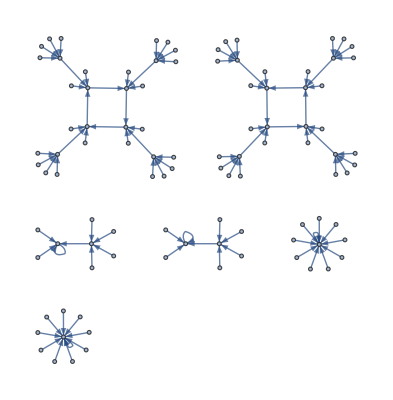
| 期望输出： |  
  | -Graphics- |

生成 50 个坐标为 0 到 10 的随机实数、半径为 0 到 2 的随机实数，随机颜色的圆的图形。»

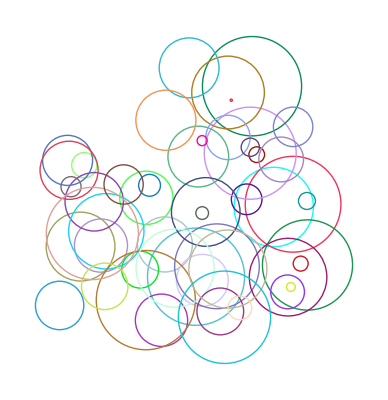
| 期望输出示例： |  
  | -Graphics- |

创建一个第 n 个素数除以 n×log(n)的图，其中 n 为 2 到 1000。»

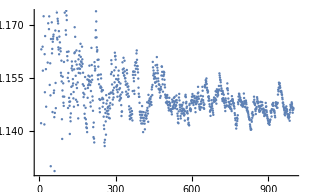
| 期望输出： |  
  | -Graphics- |

将 100 以内的连续素数之间的差值绘制为线条图。»

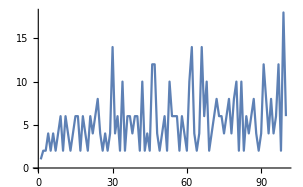
| 期望输出： |  
  | -Graphics- |

生成一个由 20 个中央 C 音符组成的序列，其持续时间随机在 0 到 0.5 秒之间。»

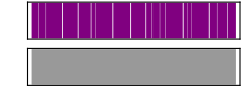
| 期望输出示例： |  
  | -Graphics- |

对最大为 50 的 i 和 j 的 Mod[i,j] 创建一个数组图示。»

| 期望输出： |  
  | -Graphics- |

创建 x^y 对 n 的模余的列表，其中 x 和 y 均为 50 以内的数，创建此列表的数组图示的列表，其中 n 从 2 到 10 之间变化。»

| 期望输出： |  
  | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} |

使用 Round 来计算 50 位 π 的小数部分。»

| 期望输出： |  
  | 0.14159265358979323846264338327950288419716939937511 |

找到前 1000 个质数的总和。»

| 期望输出： |  
  | 3682913 |

创建前 100 个质数对 4 模余的列表。»

| 期望输出： |  
  | {2,3,1,3,3,1,1,3,3,1,3,1,1,3,3,1,3,1,3,3,1,3,3,1,1,1,3,3,1,1,3,3,1,3,1,3,1,3,3,1,3,1,3,1,1,3,3,3,3,1,1,3,1,3,1,3,1,3,1,1,3,1,3,3,1,1,3,1,3,1,1,3,3,1,3,3,1,1,1,1,3,1,3,1,3,3,1,1,1,3,3,3,3,3,3,3,1,1,3,1} |

创建前 10000 个素数对 4 的模余，将它们乘以 90°，并使用它们创建一个角度路径。»

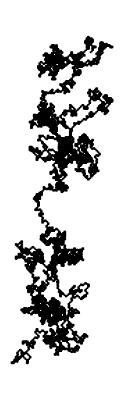
| 期望输出： |  
  | -Graphics- |

问&答

Wolfram 语言中的数学函数的例子有哪些？

标准的校内数学，比如 Sin、Cos、ArcTan、Exp 以及 GCD、Factorial、Fibonaccii。还有物理学、工程学和高等数学，比如 Gamma(伽玛函数 )、BesselJ(贝塞尔函数)、EllipticK(椭圆积分)、Zeta(黎曼 ζ 函数)、PrimePi 以及 EulerPhi.。统计学方面，比如 Erf、NormalDistribution、ChiSquareDistribution。总共有几百个函数。

什么是一个数字的有效数字？

它是指数字中的总位数。 N[100/3,5] 将给出 33.333，它共有 5 位有效数字。数字 100/3 是精确值；N[100/3,5] 将把其近似为 5 位有效数字。

长数字中每行末尾的  是什么意思？

它的存在是为了显示数字将在下一行继续，与文本中的连字符相似。

我可以用 10 以外的进制吗？

是的。输入一个 16 进制的数字的方式为 16^^ffa5。使用 IntegerDigits[655,16] 来找出各位数字。

Wolfram 语言能处理复数吗？

当然可以。符号 I (大写的“i”)表示的是 −1 的平方根。

为什么 N[1.5/7,100] 没有给我一个 100 位数的结果？

因为 1.5 是一个近似的数字，精度远低于 100 位数。而像 N[15/70,100] 这样的输入将给出一个 100 位数精度的数字。

技术笔记

Wolfram 语言做的是“任意精度计算”，这意味着它可以在一个数字中保留你想要的任何位数。

当你用 N 生成一个具有一定精度的数字时，Wolfram 语言会自动跟踪该精度是如何影响计算的，所以你不必自己进行圆整误差的数值分析。

如果你输入一个像 1.5 这样的数字，它就会被认为是在你的计算机上的原始“机器精度”的数字(通常约为 16 位，尽管通常只显示 6 位)。使用 1.5`100 来指定 100 位的精度。

对于精确的输入(比如 4、2/3 或 Pi)，Wolfram 语言将总是尝试给出精确的输出。但如果输入包含近似的数字(如 2.3)，或如果你使用 N,，它就将使用近似数字。

数值近似往往是使大规模计算变得可行的关键。

PrimeQ 用于测试一个数字是否是素数(详见第 28 节)。 FactorInteger 将找出整数的因子。

RandomReal 可以给出不仅仅是均匀分布的数字。例如，RandomReal[NormalDistribution[ ]] 将给出正态分布的数字。

Round 将四舍五入到最接近的整数(向上或向下都有可能)；Floor 总是取整；Ceiling 总是向上取整。

RealDigits 是实数方面与 IntegerDigits 相似的函数。

探索更多

Wolfram 语言中的数值计算指南 »

Wolfram 语言中的数学函数指南 »